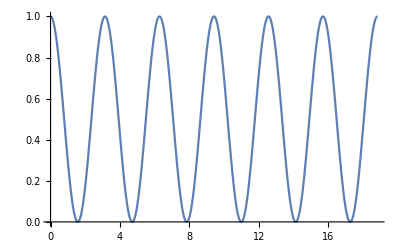

```mathematica
Plot[Cos[x]*Cos[x],{x,0,6Pi}]
```

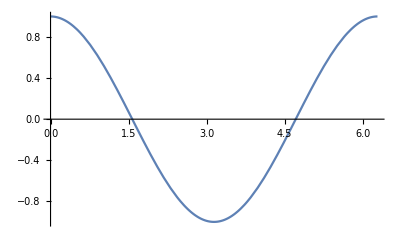

```mathematica
Plot[Cos[x],{x,0,2Pi}]
```

```mathematica
data=Table[Cos[x],{x,20Pi}]
```

{Cos[1],Cos[2],Cos[3],Cos[4],Cos[5],Cos[6],Cos[7],Cos[8],Cos[9],Cos[10],Cos[11],Cos[12],Cos[13],Cos[14],Cos[15],Cos[16],Cos[17],Cos[18],Cos[19],Cos[20],Cos[21],Cos[22],Cos[23],Cos[24],Cos[25],Cos[26],Cos[27],Cos[28],Cos[29],Cos[30],Cos[31],Cos[32],Cos[33],Cos[34],Cos[35],Cos[36],Cos[37],Cos[38],Cos[39],Cos[40],Cos[41],Cos[42],Cos[43],Cos[44],Cos[45],Cos[46],Cos[47],Cos[48],Cos[49],Cos[50],Cos[51],Cos[52],Cos[53],Cos[54],Cos[55],Cos[56],Cos[57],Cos[58],Cos[59],Cos[60],Cos[61],Cos[62]}

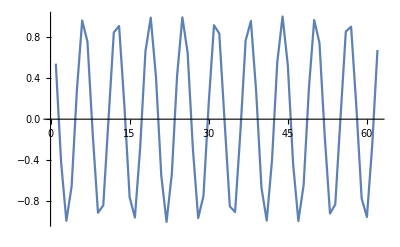

```mathematica
ListLinePlot[data]
```

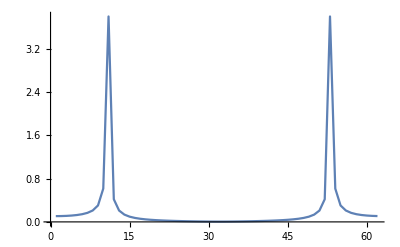

```mathematica
ListLinePlot[Abs[Fourier[data]],PlotRange->All]
```

```mathematica
ListLinePlot[Abs[InverseFourier[data]],PlotRange->All]
```

-Graphics-